# Noncontextual bound of XYZ uncertainty relation

## code for the proof

### special case

```mathematica
vp=1.1/3({{1, -1, 1}, {-1, -1, 1}, {-1, -1, -1}, {1, -1, -1}});vq=1.1/3({{1, 1, 1}, {-1, 1, 1}, {-1, 1, -1}, {1, 1, -1}});Subscript[p, x_]:=Text[Style[Subscript["P", x],Bold,FontSize->14],vp[[x]]];
Subscript[q, x_]:=Text[Style[Subscript["Q", x],Bold,FontSize->14],vq[[x]]];
cube=Graphics3D[{Subscript[p, 1],Subscript[p, 2],Subscript[p, 3],Subscript[p, 4],Subscript[q, 1],Subscript[q, 2],Subscript[q, 3],Subscript[q, 4],Opacity[0.4],Gray,Cube[2/3]}];(*use a cuboid to be less cube, remove the 8hedron, same style of fig.3*)
sph=Graphics3D[{Opacity[0.1],Red,Sphere[{0,0,0},1]}];
oct=Graphics3D[{Opacity[0.2],Yellow,Octahedron[√2]}];
exp=Graphics3D[{Thick,Line[{{0,0,0},{1/3,1/3,1/3}}]}];
Show[sph,cube,exp,oct]
```

-Graphics3D-

It is enough the permutation matrix S to generate all the preparations P_i (i=2,3,4) starting from P_1, and observing that to satisfy the “rectangular conditions” Q_i:=RotateRight[P_i];

```mathematica
Subscript[P, 1]={({{e, f}, {g, h}}),({{a, b}, {c, d}})};
x={({{0, 1}, {0, 1}}),({{0, 1}, {0, 1}})};y={({{1, 1}, {1, 1}}),({{0, 0}, {0, 0}})};(*y={({{1, 0}, {0, 1}}),({{1, 0}, {0, 1}})}*)
z={({{1, 1}, {0, 0}}),({{1, 1}, {0, 0}})};
id={({{1, 1}, {1, 1}}),({{1, 1}, {1, 1}})};
S=({{0, 1}, {1, 0}});
Subscript[P, 2]=#.S&/@Subscript[P, 1];
Subscript[P, 3]=S.#.S&/@Subscript[P, 1];
Subscript[P, 4]=S.#&/@Subscript[P, 1];
Subscript[Q, x_]:=RotateRight[Subscript[P, x]];
rep[P_]:=MatrixForm/@P
```

The preparation P_i and Q_i are

```mathematica
Table[rep[Subscript[P, i]],{i,4}]
Table[rep[Subscript[Q, i]],{i,4}]
```

{{(e | f
g | h),(a | b
c | d)},{(f | e
h | g),(b | a
d | c)},{(h | g
f | e),(d | c
b | a)},{(g | h
e | f),(c | d
a | b)}}

{{(a | b
c | d),(e | f
g | h)},{(b | a
d | c),(f | e
h | g)},{(d | c
b | a),(h | g
f | e)},{(c | d
a | b),(g | h
e | f)}}

We check that the rectangular symmetries are satisfied ( for example  ξ_(1|z)·μ_P_1=Total[Flatten[z P_1]] and ξ_(-1|z)·μ_P_3=Total[Flatten[(id-z) P_3]])

```mathematica
Total[Flatten[z Subscript[P, 1]]]==Total[Flatten[z Subscript[P, 2]]]==Total[Flatten[(id-z) Subscript[P, 3]]]==Total[Flatten[(id-z) Subscript[P, 4]]]==Total[Flatten[z Subscript[Q, 1]]]==Total[Flatten[z Subscript[Q, 2]]]==Total[Flatten[(id-z) Subscript[Q, 3]]]==Total[Flatten[(id-z) Subscript[Q, 4]]]
```

True

```mathematica
Total[Flatten[x Subscript[P, 1]]]==Total[Flatten[(id-x) Subscript[P, 2]]]==Total[Flatten[(id-x) Subscript[P, 3]]]==Total[Flatten[x Subscript[P, 4]]]==Total[Flatten[x Subscript[Q, 1]]]==Total[Flatten[(id-x) Subscript[Q, 2]]]==Total[Flatten[(id-x) Subscript[Q, 3]]]==Total[Flatten[x Subscript[Q, 4]]]
```

True

```mathematica
Total[Flatten[(id-y) Subscript[P, 1]]]==Total[Flatten[(id-y) Subscript[P, 2]]]==Total[Flatten[(id-y) Subscript[P, 3]]]==Total[Flatten[(id-y)Subscript[P, 4]]]==Total[Flatten[y Subscript[Q, 1]]]==Total[Flatten[y Subscript[Q, 2]]]==Total[Flatten[y Subscript[Q, 3]]]==Total[Flatten[y Subscript[Q, 4]]]
```

True

PNC and normalization gives us d+e=c+f=b+g=a+h=1/4, as you can check element-wise in the following

```mathematica
(**)
```

```mathematica
rep[1/2 Subscript[P, 4]+1/2 Subscript[Q, 2]]
rep[1/4 Subscript[P, 4]+1/4 Subscript[Q, 1]+1/4 Subscript[Q, 4]+1/4 Subscript[P, 1]]
```

{(b/2+g/2 | a/2+h/2
d/2+e/2 | c/2+f/2),(c/2+f/2 | d/2+e/2
a/2+h/2 | b/2+g/2)}

{(a/4+c/4+e/4+g/4 | b/4+d/4+f/4+h/4
a/4+c/4+e/4+g/4 | b/4+d/4+f/4+h/4),(a/4+c/4+e/4+g/4 | b/4+d/4+f/4+h/4
a/4+c/4+e/4+g/4 | b/4+d/4+f/4+h/4)}

```mathematica
rep[Subscript[P, 1]+Subscript[Q, 3]]
rep[Subscript[P, 2]+Subscript[Q, 4]]
rep[Subscript[P, 3]+Subscript[Q, 1]]
rep[Subscript[P, 4]+Subscript[Q, 2]]
```

{(d+e | c+f
b+g | a+h),(a+h | b+g
c+f | d+e)}

{(c+f | d+e
a+h | b+g),(b+g | a+h
d+e | c+f)}

{(a+h | b+g
c+f | d+e),(d+e | c+f
b+g | a+h)}

{(b+g | a+h
d+e | c+f),(c+f | d+e
a+h | b+g)}

```mathematica
rep[(2(x+y+z)-3id) Subscript[Q, 1]]
```

{(a | 3 b
-c | d),(-e | f
-3 g | -h)}

Above we express func=⟨X⟩+⟨Y⟩+⟨Z⟩=[2(ξ_(1|x)+ξ_(1|y)+ξ_(1|z))-3id]q_1

```mathematica
func[a_,b_,c_,d_,e_,f_,g_,h_]:=Total[Flatten[(2(x+y+z)-3id) Subscript[Q, 1]]]
func0[a_,b_,c_,d_,e_,f_,g_,h_]:=Total[Flatten[(2(x+z)-2id) Subscript[Q, 1]]]
```

```mathematica
func[a,b,c,d,e,f,g,h]
```

a+3 b-c+d-e+f-3 g-h

This is the 2D case

```mathematica
func0[a,b,c,d,e,f,g,h]
```

2 b-2 c+2 f-2 g

```mathematica
({{0, 2}, {-2, 0}})({{a, b}, {c, d}})=2(b-c)
```

2 (b-c)

```mathematica
rep[(2(x+z)-2id)]
```

{(0 | 2
-2 | 0),(0 | 2
-2 | 0)}

a+b+c+d+e+f+g+h=4(a+h)

Here the result including all the conditions

```mathematica
func[a,b,c,d,e,f,g,h]
```

a+3 b-c+d-e+f-3 g-h

```mathematica
max=Maximize[{func[a,b,c,d,e,f,g,h],a+h== 1/4,b+g== 1/4,c+f== 1/4,d+e== 1/4,a+c+e+g==1/2,b+d+f+h==1/2,a≥ 0,b≥ 0,c≥ 0,d≥ 0,e≥ 0,f≥ 0,g≥ 0,h≥ 0},{a,b,c,d,e,f,g,h}]
```

{1,{a→1/4,b→1/4,c→1/4,d→1/4,e→0,f→0,g→0,h→0}}

in max0 I am playing, but this is not essential

```mathematica
max0=Maximize[{func0[a,b,c,d,e,f,g,h],a+h== 1/4,b+g== 1/4,c+f== 1/4,d+e== 1/4,b+f<=1/2,a+e<=1/2,c+g<=1/2,d+h<=1/2,a≥ 0,b≥ 0,c≥ 0,d≥ 0,e≥ 0,f≥ 0,g≥ 0,h≥ 0},{a,b,c,d,e,f,g,h}]
```

{1,{a→1/4,b→1/4,c→0,d→1/4,e→0,f→1/4,g→0,h→0}}

This are the configuration of the epistemic states that maximize our relation

```mathematica
Table[rep[Subscript[P, i]]/.max[[2]],{i,4}]
Table[rep[Subscript[Q, i]]/.max[[2]],{i,4}]
```

{{(0 | 1/4
0 | 0),(1/4 | 1/4
0 | 1/4)},{(1/4 | 0
0 | 0),(1/4 | 1/4
1/4 | 0)},{(0 | 0
1/4 | 0),(1/4 | 0
1/4 | 1/4)},{(0 | 0
0 | 1/4),(0 | 1/4
1/4 | 1/4)}}

{{(1/4 | 1/4
0 | 1/4),(0 | 1/4
0 | 0)},{(1/4 | 1/4
1/4 | 0),(1/4 | 0
0 | 0)},{(1/4 | 0
1/4 | 1/4),(0 | 0
1/4 | 0)},{(0 | 1/4
1/4 | 1/4),(0 | 0
0 | 1/4)}}

In the following the construction of the picture of the configuration of the epistemic states that maximize our relation: we notice that we do not touch the surface of the sphere but the 8 points are out of the octahedron

```mathematica
Subscript[μQ, i_]:={Total[Flatten[(2 x-id)Subscript[Q, i]]],Total[Flatten[(2 y-id)Subscript[Q, i]]],Total[Flatten[(2 z-id)Subscript[Q, i]]]};
Subscript[μP, i_]:={Total[Flatten[(2 x-id)Subscript[P, i]]],Total[Flatten[(2 y-id)Subscript[P, i]]],Total[Flatten[(2 z-id)Subscript[P, i]]]};
```

```mathematica
Subscript[μP, 2]/.max[[2]]
```

{-1/2,-1/2,1/2}

```mathematica
√Total[vpμ[[1]]^2]
```

(√3)/2

```mathematica
vpμ=Table[Subscript[μP, i],{i,4}]/.max[[2]];vqμ=Table[Subscript[μQ, i],{i,4}]/.max[[2]];
Subscript[μp, x_]:=Text[Style[Subscript["P", x],Bold,FontSize->14],vpμ[[x]]];
Subscript[μq, x_]:=Text[Style[Subscript["Q", x],Bold,FontSize->14],vqμ[[x]]];
cubeμ=Graphics3D[{Subscript[μp, 1],Subscript[μp, 2],Subscript[μp, 3],Subscript[μp, 4],Subscript[μq, 1],Subscript[μq, 2],Subscript[μq, 3],Subscript[μq, 4],Opacity[0.4],Gray,Cube[√(4/3 Total[vpμ[[1]]^2])]}];
sph=Graphics3D[{Opacity[0.1],Red,Sphere[{0,0,0},1]}];
oct=Graphics3D[{Opacity[0.2],Yellow,Octahedron[√2]}];
exp=Graphics3D[{Thick,Line[{{0,0,0},{1/3,1/3,1/3}}]}];
Show[sph,cubeμ,exp,oct]
```

-Graphics3D-

Assuming that Q_1 is the preparation with the all positive expectation values then max⟨X⟩+⟨Y⟩+⟨Z⟩=3/2.

### general case

It is enough the permutation matrix S to generate all the preparations P_i (i=2,3,4) starting from P_1, and observing that to satisfy the “rectangular conditions” Q_i:=RotateRight[P_i];

```mathematica
Subscript[P, 1]={({{e, f}, {g, h}}),({{a, b}, {c, d}})};
c[x_]:={({{Subscript[x, e], Subscript[x, f]}, {Subscript[x, g], Subscript[x, h]}}),({{Subscript[x, a], Subscript[x, b]}, {Subscript[x, c], Subscript[x, d]}})};
x={({{0, 1}, {0, 1}}),({{0, 1}, {0, 1}})};y={({{1, 1}, {1, 1}}),({{0, 0}, {0, 0}})};(*y={({{1, 0}, {0, 1}}),({{1, 0}, {0, 1}})}*)
z={({{1, 1}, {0, 0}}),({{1, 1}, {0, 0}})};
id={({{1, 1}, {1, 1}}),({{1, 1}, {1, 1}})};
S=({{0, 1}, {1, 0}});
Subscript[P, 2]=#.S&/@(Subscript[P, 1]+c[ϵ]);
Subscript[P, 3]=S.#.S&/@(Subscript[P, 1]+c[η]);
Subscript[P, 4]=S.#&/@(Subscript[P, 1]+c[δ]);
Subscript[Q, 1]=RotateRight[Subscript[P, 1]+c[υ]];
Subscript[Q, 2]=RotateRight[S.#.S&/@(Subscript[P, 1]+c[ζ])];
Subscript[Q, 3]=RotateRight[S.#.S&/@(Subscript[P, 1]+c[ν])];
Subscript[Q, 4]=RotateRight[S.#.S&/@(Subscript[P, 1]+c[ι])];
rep[P_]:=MatrixForm/@P
```

The preparation P_i and Q_i are

```mathematica
Table[rep[Subscript[P, i]],{i,4}]
Table[rep[Subscript[Q, i]],{i,4}]
```

{{(e | f
g | h),(a | b
c | d)},{(f+ϵ_f | e+ϵ_e
h+ϵ_h | g+ϵ_g),(b+ϵ_b | a+ϵ_a
d+ϵ_d | c+ϵ_c)},{(h+η_h | g+η_g
f+η_f | e+η_e),(d+η_d | c+η_c
b+η_b | a+η_a)},{(g+δ_g | h+δ_h
e+δ_e | f+δ_f),(c+δ_c | d+δ_d
a+δ_a | b+δ_b)}}

{{(a+υ_a | b+υ_b
c+υ_c | d+υ_d),(e+υ_e | f+υ_f
g+υ_g | h+υ_h)},{(d+ζ_d | c+ζ_c
b+ζ_b | a+ζ_a),(h+ζ_h | g+ζ_g
f+ζ_f | e+ζ_e)},{(d+ν_d | c+ν_c
b+ν_b | a+ν_a),(h+ν_h | g+ν_g
f+ν_f | e+ν_e)},{(d+ι_d | c+ι_c
b+ι_b | a+ι_a),(h+ι_h | g+ι_g
f+ι_f | e+ι_e)}}

We impose the normalization and the rectangular symmetries  ( for example  ξ_(1|z)·μ_P_1=Total[Flatten[z P_1]] and ξ_(-1|z)·μ_P_3=Total[Flatten[(id-z) P_3]])

```mathematica
norm=Flatten@Table[{Total[Flatten[Subscript[P, i]]]==1,Total[Flatten[Subscript[Q, i]]]==1},{i,4}];
```

{a+b+c+d+e+f+g+h==1,a+b+c+d+e+f+g+h+υ_a+υ_b+υ_c+υ_d+υ_e+υ_f+υ_g+υ_h==1,a+b+c+d+e+f+g+h+ϵ_a+ϵ_b+ϵ_c+ϵ_d+ϵ_e+ϵ_f+ϵ_g+ϵ_h==1,a+b+c+d+e+f+g+h+ζ_a+ζ_b+ζ_c+ζ_d+ζ_e+ζ_f+ζ_g+ζ_h==1,a+b+c+d+e+f+g+h+η_a+η_b+η_c+η_d+η_e+η_f+η_g+η_h==1,a+b+c+d+e+f+g+h+ν_a+ν_b+ν_c+ν_d+ν_e+ν_f+ν_g+ν_h==1,a+b+c+d+e+f+g+h+δ_a+δ_b+δ_c+δ_d+δ_e+δ_f+δ_g+δ_h==1,a+b+c+d+e+f+g+h+ι_a+ι_b+ι_c+ι_d+ι_e+ι_f+ι_g+ι_h==1}

```mathematica
symmZ1={
Total[Flatten[z Subscript[P, 1]]]==Total[Flatten[z Subscript[P, 2]]],
Total[Flatten[z Subscript[P, 2]]]==Total[Flatten[(id-z) Subscript[P, 3]]],
Total[Flatten[(id-z) Subscript[P, 3]]]==Total[Flatten[(id-z) Subscript[P, 4]]],
Total[Flatten[(id-z) Subscript[P, 4]]]==Total[Flatten[z Subscript[Q, 1]]],
Total[Flatten[z Subscript[Q, 1]]]==Total[Flatten[z Subscript[Q, 2]]],
Total[Flatten[z Subscript[Q, 2]]]==Total[Flatten[(id-z) Subscript[Q, 3]]],
Total[Flatten[(id-z) Subscript[Q, 3]]]==Total[Flatten[(id-z) Subscript[Q, 4]]]};
symmX1={Total[Flatten[x Subscript[P, 1]]]==Total[Flatten[(id-x) Subscript[P, 2]]],
Total[Flatten[(id-x) Subscript[P, 2]]]==Total[Flatten[(id-x) Subscript[P, 3]]],
Total[Flatten[(id-x) Subscript[P, 3]]]==Total[Flatten[x Subscript[P, 4]]],
Total[Flatten[x Subscript[P, 4]]]==Total[Flatten[x Subscript[Q, 1]]],
Total[Flatten[x Subscript[Q, 1]]]==Total[Flatten[(id-x) Subscript[Q, 2]]],
Total[Flatten[(id-x) Subscript[Q, 2]]]==Total[Flatten[(id-x) Subscript[Q, 3]]],
Total[Flatten[(id-x) Subscript[Q, 3]]]==Total[Flatten[x Subscript[Q, 4]]]};
symmY1={Total[Flatten[(id-y) Subscript[P, 1]]]==Total[Flatten[(id-y) Subscript[P, 2]]],
Total[Flatten[(id-y) Subscript[P, 2]]]==Total[Flatten[(id-y) Subscript[P, 3]]],
Total[Flatten[(id-y) Subscript[P, 3]]]==Total[Flatten[(id-y)Subscript[P, 4]]],
Total[Flatten[(id-y)Subscript[P, 4]]]==Total[Flatten[y Subscript[Q, 1]]],
Total[Flatten[y Subscript[Q, 1]]]==Total[Flatten[y Subscript[Q, 2]]],
Total[Flatten[y Subscript[Q, 2]]]==Total[Flatten[y Subscript[Q, 3]]],
Total[Flatten[y Subscript[Q, 3]]]==Total[Flatten[y Subscript[Q, 4]]]};
```

We impose the noncontextual preparation conditions

```mathematica
rep[1/2 Subscript[P, 4]+1/2 Subscript[Q, 2]];
rep[1/4 Subscript[P, 4]+1/4 Subscript[Q, 1]+1/4 Subscript[Q, 4]+1/4 Subscript[P, 1]];
rep[Subscript[P, 1]+Subscript[Q, 3]];
rep[Subscript[P, 2]+Subscript[Q, 4]];
rep[Subscript[P, 3]+Subscript[Q, 1]];
rep[Subscript[P, 4]+Subscript[Q, 2]];
eq[P_,Q_]:=MapThread[(#1==#2)& ,{P,Q},3]
```

```mathematica
nc1=Flatten@eq[1/2 Subscript[P, 4]+1/2 Subscript[Q, 2],1/4 Subscript[P, 4]+1/4 Subscript[Q, 1]+1/4 Subscript[Q, 4]+1/4 Subscript[P, 1]];
nc2=Flatten@eq[1/2 Subscript[P, 1]+1/2 Subscript[Q, 3],1/4 Subscript[P, 4]+1/4 Subscript[Q, 1]+1/4 Subscript[Q, 4]+1/4 Subscript[P, 1]];
nc3=Flatten@eq[1/2 Subscript[P, 2]+1/2 Subscript[Q, 4],1/4 Subscript[P, 4]+1/4 Subscript[Q, 1]+1/4 Subscript[Q, 4]+1/4 Subscript[P, 1]];
nc4=Flatten@eq[1/2 Subscript[P, 3]+1/2 Subscript[Q, 1],1/4 Subscript[P, 4]+1/4 Subscript[Q, 1]+1/4 Subscript[Q, 4]+1/4 Subscript[P, 1]];
pos=Flatten@Table[{Flatten[Map[#>= 0&,Subscript[P, i],{3}]],Flatten[Map[#>= 0&,Subscript[Q, i],{3}]]},{i,4}];
```

Above we express func=|⟨X⟩|+|⟨Y⟩|+|⟨Z⟩|=[2(ξ_(1|x)+ξ_(1|y)+ξ_(1|z))-3id]Q_1

```mathematica
func[a_,b_,c_,d_,e_,f_,g_,h_]:=Total[Flatten[(2(x+y+z)-3id) Subscript[Q, 1]]]
```

```mathematica
cond=Join[{func[a,b,c,d,e,f,g,h]},norm,symmX1,symmY1,symmZ1,nc1,nc2,nc3,nc4,pos];
var=Flatten[{Subscript[P, 1],c[ϵ],c[η],c[δ],c[ν],c[ζ],c[υ],c[ι]}];
```

```mathematica
func[a,b,c,d,e,f,g,h]
```

a-c+d-e+f-h+υ_a+3 (b+υ_b)-υ_c+υ_d-υ_e+υ_f-3 (g+υ_g)-υ_h

```mathematica
max=NMaximize[cond,var]
```

{1.,{e→0.5,f→0.,g→0.,h→0.,a→0.,b→0.5,c→0.,d→0.,ϵ_e→-0.5,ϵ_f→0.5,ϵ_g→0.,ϵ_h→0.,ϵ_a→0.5,ϵ_b→-0.5,ϵ_c→0.,ϵ_d→0.,η_e→0.,η_f→0.,η_g→0.,η_h→0.,η_a→0.,η_b→0.,η_c→0.,η_d→0.,δ_e→-0.5,δ_f→0.5,δ_g→0.,δ_h→0.,δ_a→0.5,δ_b→-0.5,δ_c→0.,δ_d→0.,ν_e→-0.5,ν_f→0.5,ν_g→0.,ν_h→0.,ν_a→0.5,ν_b→-0.5,ν_c→0.,ν_d→0.,ζ_e→-0.5,ζ_f→0.,ζ_g→0.5,ζ_h→0.,ζ_a→0.,ζ_b→-0.5,ζ_c→0.,ζ_d→0.5,υ_e→-0.5,υ_f→0.5,υ_g→0.,υ_h→0.,υ_a→0.5,υ_b→-0.5,υ_c→0.,υ_d→0.,ι_e→-0.5,ι_f→0.5,ι_g→0.,ι_h→0.,ι_a→0.5,ι_b→-0.5,ι_c→0.,ι_d→0.}}

The epistemic states that realize the maximum are

```mathematica
Table[rep[Subscript[P, i]],{i,4}]/.max[[2]]
Table[rep[Subscript[Q, i]],{i,4}]/.max[[2]]
```

{{(0.5 | 0.
0. | 0.),(0. | 0.5
0. | 0.)},{(0.5 | 0.
0. | 0.),(0. | 0.5
0. | 0.)},{(0. | 0.
0. | 0.5),(0. | 0.
0.5 | 0.)},{(0. | 0.
0. | 0.5),(0. | 0.
0.5 | 0.)}}

{{(0.5 | 0.
0. | 0.),(0. | 0.5
0. | 0.)},{(0.5 | 0.
0. | 0.),(0. | 0.5
0. | 0.)},{(0. | 0.
0. | 0.5),(0. | 0.
0.5 | 0.)},{(0. | 0.
0. | 0.5),(0. | 0.
0.5 | 0.)}}

In the following the construction of the picture of the configuration of the epistemic states that maximize our relation

```mathematica
Subscript[μQ, i_]:={Total[Flatten[(2 x-id)Subscript[Q, i]]],Total[Flatten[(2 y-id)Subscript[Q, i]]],Total[Flatten[(2 z-id)Subscript[Q, i]]]};
Subscript[μP, i_]:={Total[Flatten[(2 x-id)Subscript[P, i]]],Total[Flatten[(2 y-id)Subscript[P, i]]],Total[Flatten[(2 z-id)Subscript[P, i]]]};
```

```mathematica
Subscript[μP, 2]/.max[[2]]
```

{0.,0.,1.}

```mathematica
vpμ=Table[Subscript[μP, i],{i,4}]/.max[[2]];vqμ=Table[Subscript[μQ, i],{i,4}]/.max[[2]];
Subscript[μp, x_]:=Text[Style[Subscript["P", x],Bold,FontSize->14],vpμ[[x]]];
Subscript[μq, x_]:=Text[Style[Subscript["Q", x],Bold,FontSize->14],vqμ[[x]]];
√Total[vpμ[[1]]^2]
cubeμ=Graphics3D[{Subscript[μp, 1],Subscript[μp, 2],Subscript[μp, 3],Subscript[μp, 4],Subscript[μq, 1],Subscript[μq, 2],Subscript[μq, 3],Subscript[μq, 4],Opacity[0.4],Gray,Cube[√(4/3 Total[vpμ[[1]]^2])]}];
sph=Graphics3D[{Opacity[0.1],Red,Sphere[{0,0,0},1]}];
oct=Graphics3D[{Opacity[0.2],Yellow,Octahedron[√2]}];
Show[sph,cubeμ,oct]
```

1.

-Graphics3D-

## Figure

```mathematica
(* uncomment if you need to install it

ResourceFunction["MaTeXInstall"][]
*)
```

PacletObject[…]

```mathematica
ConfigureMaTeX["pdfLaTeX"->"C:\\texlive\\2022\\bin\\win32\\pdflatex.exe","Ghostscript"->"C:\\Program Files\\gs\\gs9.56.1\\bin\\gswin64c.exe"]
```

{CacheSize→100,WorkingDirectory→Automatic,pdfLaTeX→C:\texlive\2022\bin\win32\pdflatex.exe,Ghostscript→C:\Program Files\gs\gs9.56.1\bin\gswin64c.exe}

```mathematica
<<MaTeX`
```

### fig 1

```mathematica
(*xyz=ParametricPlot3D[{{Cos[t], Sin[t],0},{0, Cos[t], Sin[t]},{ Cos[t],0,Sin[t]}},{t,0,2 π},PlotStyle->{{Black,Thick,Dashed},{Black,Thick,Dashed},{Black,Thick,Dashed}}];*)
```

```mathematica
l=1.5;vp={1.3,.5,.8};op=.5;offsetlabel=.15;
axes0={Black,Thick,Opacity[1],
Arrowheads[{.03}],Arrow[Tube[{{-l,0,0},{l,0,0}}]],
Arrowheads[{.03}],Arrow[Tube[{{0,-l,0},{0,l,0}}]],
Arrowheads[{.03}],Arrow[Tube[{{0,0,-l},{0,0,l}}]],Text[Style[MaTeX["\\hat z",Magnification->3]], {0,0,l+offsetlabel}],
Text[Style[MaTeX["\\hat y",Magnification->3]], {0,l+offsetlabel,0}],
Text[Style[MaTeX["\\hat x",Magnification->3]], {l+offsetlabel,0,0}]};
sph[opacity_,color_,s_,n_,r_:1]:={Opacity[opacity],color,Specularity[s,n],Sphere[{0,0,0},r]}
fig1a=Graphics3D[Join[axes0,sph[op,Blue,1,5,1],{Opacity[0],Cube[2]}],Boxed->False,ViewPoint->vp]
oct1={Opacity[op],Blue,Octahedron[√2]};
fig1b=Graphics3D[Join[axes0,oct1,{Opacity[.0],Cube[2]}],Boxed->False,ViewPoint->vp]
fig1c=Graphics3D[Join[axes0,sph[op,Blue,1,5,0.5],{Opacity[0],White,Cube[2]}],Boxed->False,ViewPoint->vp]
fig1d=Graphics3D[Join[axes0,{Opacity[op],Blue,Cube[2]}],Boxed->False,ViewPoint->vp]
tetra={Opacity[op],Blue,Tetrahedron[{{1,1,1},{1,-1,-1},{-1,-1,1},{-1,1,-1}}]};
fig1e=Graphics3D[Join[axes0,tetra,{Opacity[.0],White,Cube[2]}],Boxed->False,ViewPoint->vp]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«2 more identical outputs»

### fig 2

#### 2d

```mathematica
(*{Line[{{0.4,0.5,0.6},{-0.4,0.5,0.6},{-0.4,0.5,-0.6},{0.4,0.5,-0.6},{0.4,0.5,0.6}}]}
Sphere[{{0.4,0.5,0.6}},.05],
Sphere[{{0.4,0.5,-0.6}},.05],
Sphere[{{-0.4,0.5,0.6}},.05],
Sphere[{{-0.4,0.5,-0.6}},.05],
*)mag=2.8;hsp[x_,y_,z_,r_:.05]:=ParametricPlot3D[{r Cos[u] Sin[v]+x,r Sin[u] Sin[v]+y,r Cos[v]+z},{u,0,π},{v,0,π},Mesh->None,Boxed->False,Axes->None,PlotStyle->Black]
plane={Red,Opacity[0.4],EdgeForm[],Cuboid[{-l-.3,0.5,-l+.3},{l-.3,-0.001+.5,l-.3}]};
points={Black,Opacity[.58],
Opacity[1],
Text[Style[MaTeX["\\vec{s}_2",Magnification->2.8]], {.5,.5,.9}],
Text[Style[MaTeX["\\vec{s}_1",Magnification->2.8]], {-.5,.5,.9}],
Text[Style[MaTeX["\\vec{s}_4",Magnification->2.8]], {.5,.5,-.9}],
Text[Style[MaTeX["\\vec{s}_3",Magnification->2.8]], {-.5,.5,-.95 }]};gr=Graphics3D[Join[axes0,sph[.3,Blue,15,6,1],plane,points],Boxed->False,ViewPoint->{1.5,.85,0.5}];
Show[gr,hsp[.4,.5,.6,.05],hsp[.4,.5,-.6,.05],hsp[-.4,.5,.6,.05],hsp[-.4,.5,-.6,.05]]
```

-Graphics3D-

#### 3d

```mathematica
l=1.5;vp={1.3,.5,.8};op=.5;offsetlabel=.14;
axes0={Black,Thick,Opacity[1],
Arrowheads[{.03}],Arrow[Tube[{{-l,0,0},{l,0,0}}]],
Arrowheads[{.03}],Arrow[Tube[{{0,-l,0},{0,l,0}}]],
Arrowheads[{.03}],Arrow[Tube[{{0,0,-l},{0,0,l}}]],Text[Style[MaTeX["\\hat z",Magnification->3]], {0,0,l+offsetlabel}],
Text[Style[MaTeX["\\hat y",Magnification->3]], {0,l+offsetlabel,0}],
Text[Style[MaTeX["\\hat x",Magnification->3]], {l+offsetlabel,0,0}]};
α=1.1/3;
xx=.9;yy=1.3;zz=1.5;
vp=({{xx, -yy, zz}, {-xx, -yy, zz}, {-xx, -yy, -zz}, {xx, -yy, -zz}});vq=({{xx, yy, zz}, {-xx, yy, zz}, {-xx, yy, -zz}, {xx, yy, -zz}});offz={0,0,.15};
Subscript[p, 1]=Text[Style[MaTeX["\\vec{s}_6",Magnification->2]],α vp[[1]]+offz];
Subscript[p, 2]=Text[Style[MaTeX["\\vec{s}_2",Magnification->2]],α vp[[2]]+offz];
{{Subscript[p, 3]=Text[Style[MaTeX["\\vec{s}_1",Magnification->2]],α vp[[3]]-offz];}, {Subscript[p, 4]=Text[Style[MaTeX["\\vec{s}_5",Magnification->2]],α vp[[4]]-offz];}}
Subscript[q, 1]=Text[Style[MaTeX["\\vec{s}_8",Magnification->2]],α vq[[1]]+offz];
Subscript[q, 2]=Text[Style[MaTeX["\\vec{s}_4",Magnification->2]],α vq[[2]]+offz];
Subscript[q, 3]=Text[Style[MaTeX["\\vec{s}_3",Magnification->2]],α vq[[3]]-offz];
Subscript[q, 4]=Text[Style[MaTeX["\\vec{s}_7",Magnification->2]],α vq[[4]]-offz];
cube=Graphics3D[{Subscript[p, 1],Subscript[p, 2],Subscript[p, 3],Subscript[p, 4],Subscript[q, 1],Subscript[q, 2],Subscript[q, 3],Subscript[q, 4],Opacity[1],Black,
Line[{1/3 vp[[1]],1/3 vp[[2]]}],
Line[{1/3 vp[[2]],1/3 vp[[3]]}],
Line[{1/3 vp[[3]],1/3 vp[[4]]}],
Line[{1/3 vp[[1]],1/3 vp[[4]]}],
Line[{1/3 vq[[1]],1/3 vq[[2]]}],
Line[{1/3 vq[[2]],1/3 vq[[3]]}],
Line[{1/3 vq[[3]],1/3 vq[[4]]}],
Line[{1/3 vq[[1]],1/3 vq[[4]]}],
Line[{1/3 vp[[1]],1/3 vq[[1]]}],Line[{1/3 vp[[2]],1/3 vq[[2]]}],Line[{1/3 vp[[3]],1/3 vq[[3]]}],Line[{1/3 vp[[4]],1/3 vq[[4]]}]
}];(*use a cuboid to be less cube, remove the 8hedron, same style of fig.3*)
sp=Graphics3D[{Opacity[0.5],Blue,Specularity[1,5],Sphere[{0,0,0},1]}];
Show[Graphics3D[axes0],sp,cube,Graphics3D[{Black,Specularity[1,20],Sphere[{1/3 vp[[1]],1/3 vp[[2]],1/3 vp[[3]],1/3 vp[[4]],1/3 vq[[1]],1/3 vq[[2]],1/3 vq[[3]],1/3 vq[[4]]},.05]}],Boxed->False,ViewPoint->{1.5,.85,0.5}]
```

{{Null},{Null}}

-Graphics3D-

```mathematica
-Graphics3D-//Options
```

{ImageSize→{370.558,413.519},ImageSizeRaw→Automatic,ViewPoint→{-0.481811,-2.62274,2.08305},ViewVertical→{0.253985,-0.0417546,0.966306}}

### fig 3

```mathematica
l=1.2;op=.8;
one[x_,y_,z_,txt_:"1"]:=Text[Style[MaTeX[txt,Magnification->2]], {x,y,z}]
axes0={Black,Thick,Opacity[1.],
Arrowheads[{.03}],Arrow[Tube[{{0,0,0},{l,0,0}}]],
Arrowheads[{.03}],Arrow[Tube[{{0,0,0},{0,l,0}}]],
Arrowheads[{.03}],Arrow[Tube[{{0,0,0},{0,0,l}}]],Text[Rotate[Style[MaTeX["| \\langle Z\\rangle|",Magnification->2]],93 Degree], {-.25,0,1/2}],
Text[Rotate[Style[MaTeX["| \\langle Y\\rangle|",Magnification->2]],20 Degree], {0,1/3,.15}],
Text[Rotate[Style[MaTeX["| \\langle X\\rangle|",Magnification->2]],-20 Degree], {1/2,-.1,-.2}],
one[-.1,0,1],one[-.04,1,.06],one[1,0,-.1],one[0,0,-.1,"0"],one[.1,0,.49,"i"],one[.1,0.1,.65,"ii"],one[.25,0.25,.72,"iii"],one[.75,0.25,.88,"iv"]};
sp=SphericalPlot3D[{1/(√3),1},{θ,0,π/2},{ϕ,0,π/2},Axes->False,PlotStyle->{{Blue,Opacity[op]},{Blue,Opacity[op]}},Mesh->None];
cube=Plot3D[UnitBox[x/2,y/2],{x,0,1.001},{y,0,1.001},PlotRange->{0,1.1},Exclusions->None,AspectRatio->1,Axes->False,PlotStyle->{Blue,Opacity[.7]},PlotPoints->80,Mesh->None];
pl=Plot3D[1-(x+y),{x,0,1.001},{y,0,1.001},PlotRange->{0,1.1},AspectRatio->1,Axes->False,PlotStyle->{Red,Opacity[0.8]},PlotPoints->80,Mesh->None];
fig3b=Show[Graphics3D[axes0],sp,cube,pl,Boxed->False,ViewPoint->{1.9401770449343725,-2.6211216955982497,0.9030138931234015}
]
```

-Graphics3D-

```mathematica
l=1.2;
one[x_,y_,z_,txt_:"1"]:=Text[Style[MaTeX[txt,Magnification->2]], {x,y,z}]
axes0={Black,Thick,Opacity[1.],
Arrowheads[{.03}],Arrow[Tube[{{0,0,0},{l,0,0}}]],
Arrowheads[{.03}],Arrow[Tube[{{0,0,0},{0,l,0}}]],
Arrowheads[{.03}],Arrow[Tube[{{0,0,0},{0,0,l}}]],Text[Rotate[Style[MaTeX["| \\langle Z\\rangle|",Magnification->2]],93 Degree], {-.25,0,1/2}],
Text[Rotate[Style[MaTeX["| \\langle Y\\rangle|",Magnification->2]],20 Degree], {0,1/3,.15}],
Text[Rotate[Style[MaTeX["| \\langle X\\rangle|",Magnification->2]],-20 Degree], {1/2,-.1,-.2}],
one[-.1,0,1],one[-.04,1,.06],one[1,0,-.1],one[0,0,-.1,"0"],one[.1,0,.49,"i"],one[.1,0.1,.65,"ii"],one[.25,0.25,.72,"iii"],one[.75,0.25,.88,"iv"]};
sp=SphericalPlot3D[{1/(√3),1},{θ,0,π/2},{ϕ,0,π/2},Axes->False,PlotStyle->{{Blue,Opacity[.8]},{Blue,Opacity[0.5]}},Mesh->None];
cube=Plot3D[UnitBox[x/2,y/2],{x,0,1.001},{y,0,1.001},PlotRange->{0,1.1},Exclusions->None,AspectRatio->1,Axes->False,PlotStyle->{Blue,Opacity[0.1]},PlotPoints->80,Mesh->None];
pl=Plot3D[1-(x+y),{x,0,1.001},{y,0,1.001},PlotRange->{0,1.1},AspectRatio->1,Axes->False,PlotStyle->{Red,Opacity[0.8]},PlotPoints->80,Mesh->None];
fig3b=Show[Graphics3D[axes0],sp,cube,pl,Boxed->False,ViewPoint->{1.9401770449343725,-2.6211216955982497,0.9030138931234015}
]
```

-Graphics3D-

```mathematica
(*to obtain the ViewPoint after we rotate manually, and overwrite it above*)
```

```mathematica
-Graphics3D-//Options
```

{Boxed→False,ImageSize→{374.078,327.68},ImageSizeRaw→Automatic,ViewPoint→{1.94018,-2.62112,0.903014},ViewVertical→{0.204293,-0.2696,0.941053}}

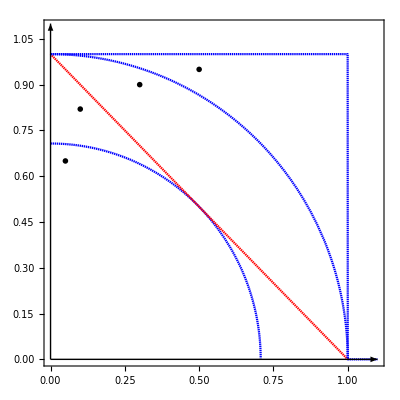

```mathematica
plot2d=Plot[{√(1/2-x^2),1-x,√(1-x^2),UnitBox[x/2]},{x,0,1.1},PlotRange->{0,1.09},Exclusions->None,AspectRatio->1,PlotStyle->{{AbsoluteDashing[{1,0}],Blue},{AbsoluteDashing[{1,0}],Red},{AbsoluteDashing[{1,0}],
 Blue},{AbsoluteDashing[{1,0}],Blue}},BaseStyle->{FontFamily->"Times",FontSize->20},PlotRangePadding->0,Frame->{{True,False},{True,False}},FrameTicksStyle->Directive[Black,Thick],FrameLabel->{MaTeX["| \\langle X\\rangle|",Magnification->2],MaTeX["| \\langle Z\\rangle|",Magnification->2]},Epilog->{Arrow[{{0,0},{1.1,0}}],Arrow[{{0,0},{0,1.1}}],
Text[MaTeX["i",Magnification->2],{.05,.65}],
Text[MaTeX["ii",Magnification->2],{.1,.82}],
Text[MaTeX["iii",Magnification->2],{.3,.9}],
Text[MaTeX["iv",Magnification->2],{.5,.95}]}]
```

```mathematica
(*for exrternal ticks marks read https://mathematica.stackexchange.com/questions/19123/how-can-automatic-ticks-be-made-outie*)
```

### fig 4

```mathematica
(*we need the 3d version of this picture*)
```

#### 2d

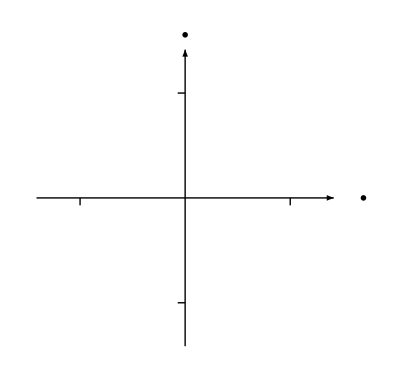

```mathematica
l=1;
one1[x_,z_,txt_:"+1"]:=Text[MaTeX[txt,Magnification->20/12],{x,z}]
labelz=MaTeX["| \\langle Z\\rangle|",Magnification->20/12];labelx=MaTeX["| \\langle X\\rangle|",Magnification->20/12];
marks=Graphics[{Line[{{l/(√2),0},{l/(√2),-.05}}],
Line[{{-l/(√2),0},{-l/(√2),-.05}}],
Line[{{0,l/(√2)},{-.05,l/(√2)}}],
Line[{{0,-l/(√2)},{-.05,-l/(√2)}}]
}];
axes=Graphics[{Black,
Arrowheads[{.03}],Arrow[{{-l,0},{l,0}}],
Arrowheads[{.03}],Arrow[{{0,-l},{0,l}}],
Text[Style[labelz], {0,l+.1 }],
Text[Style[labelx], {l+.2,0}],EdgeForm[Directive[Thickness[.005],Red]],White,Opacity[0.],Rotate[Rectangle[{-(√l)/2,-(√l)/2},{(√l)/2,(√l)/2}],π/4,{0,0}],
one1[.75,-.15],one1[-.15,.75],one1[-.15,-.75,"-1"],one1[-.75,-.15,"-1"],
Line[{{0,.75},{-1,.75}},{{0,.75},{-1,.75}}]}];
Show[axes,marks]
```

#### 3d

```mathematica
one[x_,y_,z_,txt_:"+1"]:=Text[Style[MaTeX[txt,Magnification->2]], {x,y,z}]
l=1.5;vp={1.3,.5,.8};op=.5;offsetlabel=.2;mag=2;
axes0={Black,Thick,Opacity[1],
Arrowheads[{.03}],Arrow[Tube[{{-l,0,0},{l,0,0}}]],
Arrowheads[{.03}],Arrow[Tube[{{0,-l,0},{0,l,0}}]],
Arrowheads[{.03}],Arrow[Tube[{{0,0,-l},{0,0,l}}]],

one[0,-.18,1],one[0,-.18,-1.18,"-1"],
one[0,1,-.18],one[0,-1.15,-.18,"-1"],
one[.9,-.25,-.15],one[-1.2,-.3,-.15,"-1"],
Text[Style[MaTeX[" \\langle Z\\rangle",Magnification->mag]], {0,0,l+offsetlabel}],
Text[Style[MaTeX[" \\langle Y\\rangle",Magnification->mag]], {0,l+offsetlabel,0}],
Text[Style[MaTeX[" \\langle X\\rangle",Magnification->mag]], {l+offsetlabel,0,0}]};
oct1={Opacity[0.1],White,EdgeForm[{Thick,Red}],Octahedron[√2]};
fig1b=Graphics3D[Join[axes0,oct1],Boxed->False,ViewPoint->vp]
```

-Graphics3D-

### fig 5

```mathematica
vec[μ3_,μ4_,μ2_,μ1_]:=({{{0,0,0}, {.8,.8,μ3}}, {{1,0,0}, {1.8,.8,μ4}}, {{0,1,0}, {.8,1.8,μ2}}, {{1,1,0}, {1.8,1.8,μ1}}})
coolegend=vec[0,0,0,0];
col={RGBColor[0,0,1,1],RGBColor[0,0,1,1],RGBColor[0,0,1,1],RGBColor[0,0,1,1]};
flegend[i_]:={EdgeForm[Directive[Thick,Cyan]],Blue,Cuboid@@coolegend[[i]]}
cubeslegend=Table[Graphics3D[flegend[i]],{i,4}];
axisX=Graphics3D[{Thickness[0.002],Black,
Text[MaTeX["X",Magnification->3],{.7,0,-.65}],
Text[MaTeX["-1",Magnification->3],{.4,0,-.25}],
Text[MaTeX["+1",Magnification->3],{1.4,0,-.25}]}];
axisZ=Graphics3D[{Thickness[0.002],Black,
Text[MaTeX["Z",Magnification->3],{-.6,1,0}],
Text[MaTeX["-1",Magnification->3],{-.27,.4,0}],
Text[MaTeX["+1",Magnification->3],{-.27,1.4,0}]}];
Show[cubeslegend,axisX,axisZ,Boxed->False]
```

-Graphics3D-

```mathematica
s=3;
S1=Array[{s,0,0}&,{4,2}];
S2=Array[{0,s,0}&,{4,2}];
(*the order is Subscript[μ, 3],Subscript[μ, 4],Subscript[μ, 2],Subscript[μ, 1] and for each μ then {Yellow,Red,Green,Cyan}*)
label={3,4,2,1};
textcoo={{0,1,-1.6},{s+0.5,1,-1.5},{1.5,s+1.2,1.9},{s+1,s+.8,2.1}};
f[j_,i_,coo_]:={EdgeForm[Directive[Thick,Cyan]],Blue,Cuboid@@coo[[j,i]],Text[Style[Subscript[MaTeX["\\vec{\\mu}",Magnification->2.5], label[[j]]],FontSize->30,Black,FontFamily->"Times"],textcoo[[j]]]}
cubes[coo_]:=Table[Graphics3D[f[j,i,coo]],{j,4},{i,4}];
```

```mathematica
(*the order is Subscript[μ, 3],Subscript[μ, 4],Subscript[μ, 2],Subscript[μ, 1] *)
coo={vec[1,1,0,0],S1+vec[1,1,0,0],S2+vec[0,0,1,1],S1+S2+vec[0,0,1,1]};coo1={vec[1,.7,.3,0],S1+vec[.7,1,0,.3],S2+vec[.3,0,1,.7],S1+S2+vec[0,.3,.7,1]};
coo2={vec[1,.3,.7,0],S1+vec[.3,1,0,.7],S2+vec[.7,0,1,.3],S1+S2+vec[0,.7,.3,1]};
coo3={vec[1,0,1,0],S1+vec[0,1,0,1],S2+vec[1,0,1,0],S1+S2+vec[0,1,0,1]};
ss0=Show[cubes[coo],Boxed->False]
ss1=Show[cubes[coo1],Boxed->False]
ss2=Show[cubes[coo2],Boxed->False]
ss3=Show[cubes[coo3],Boxed->False]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

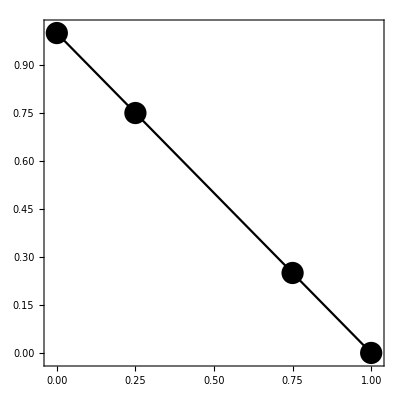

```mathematica
plot2d=Plot[1-x,{x,-0.02,1.02},Exclusions->None,AspectRatio->1,PlotStyle->{Black},BaseStyle->{FontFamily->"Modern No. 20",FontSize->20},PlotRangePadding->0,Frame->{{True,False},{True,False}},FrameTicksStyle->Directive[Black,Thick],FrameLabel->{MaTeX["| \\langle X\\rangle|",Magnification->2],MaTeX["| \\langle Z\\rangle|",Magnification->2]},Epilog->{PointSize[0.04],Point[{{0,1},{0.25,0.75},{0.75,0.25},{1,0}}]}]
```